# Scalar scattering with the John interaction

Tree-level p1 + p2 → p3 + p4 scattering of identical real scalars with arbitrary mass m. The action contains the canonical massive scalar coupled to GR and the John term beta G^(mu nu) partial_mu phi partial_nu phi, with no extra factor of 1/2 and no scalar self-potential. Start in a fresh kernel and evaluate from top to bottom. This example follows example 09 and uses the same momentum and amplitude conventions.

## 1. Load FeynGrav

```mathematica
$LoadAddOns = {"FeynArts"};
<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

Feynman rules for gravity and matter, with FeynCalc notation and FORM support through CalcFormConverter.

The default libraries include cubic and quartic graviton vertices and scalar, Dirac fermion and vector interactions with up to two gravitons. Use the FeynGravImport* commands to load additional libraries.

FeynArts supported models

• Pure general relativity

• Scalar field with a potential minimally coupled to gravity

• Scalar field with a non-minimal kinetic coupling

• Einstein-scalar-Gauss-Bonnet model

The supplied models retain interactions through order κ^2 per vertex. Use matching Model and GenericModel names with FeynCalc-patched FeynArts in a fresh kernel. Models are not initialised automatically.

Evaluate FeynGravCommands[] to list available commands, FeynGravConventions[] to inspect conventions and current settings, and FeynGravHowToCite[] for citation guidance.

## 2. Load the FeynArts model

```mathematica
model = "John";
```

## 3. Generate and display the diagrams

There are three graviton-exchange diagrams, in the s, t and u channels. Each vertex combines the minimal and John contributions. There is no four-scalar contact or scalar self-interaction exchange. The gravitational ghost does not contribute to this tree. The hh phi phi vertex cannot contribute to a four-scalar tree.

```mathematica
topologies = CreateTopologies[0, 2 -> 2, Adjacencies -> {3, 4}];
insertions = InsertFields[topologies, {S[1], S[1]} -> {S[1], S[1]}, Model -> model, GenericModel -> model, InsertionLevel -> {Classes}];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/John/John.gen

> $GenericMixing is OFF

generic model {John} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/John/John.mod

> 4 particles (incl. antiparticles) in 3 classes

> $CounterTerms are ON

> 5 vertices

classes model {John} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 3 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

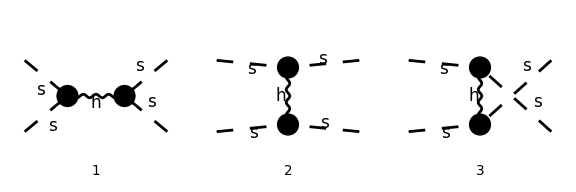

```mathematica
Paint[insertions, ColumnsXRows -> {3, 1}, Numbering -> Simple, SheetHeader -> "John: scalar scattering", DisplayFunction -> (Print /@ Render[#, ImageSize -> {576, 192}] &)];
```

## 4. Fix the on-shell kinematics

p1 and p2 are incoming; p3 and p4 are outgoing. SetMandelstam uses the all-incoming list p1, p2, -p3, -p4. All four scalars have mass m, and s + t + u = 4 m^2. The calculation below is a four-dimensional tree amplitude. Scalar-product assignments persist in the kernel.

```mathematica
FCClearScalarProducts[];
SetMandelstam[s, t, u, p1, p2, -p3, -p4, m, m, m, m];
```

## 5. Calculate the on-shell amplitude

The single command below constructs, converts and contracts the diagrams with the on-shell scalar products already assigned. The Feynman rules yield i M, so division by I defines M. ScalarMass and JohnBeta are replaced by m and the Greek symbol beta. ChangeDimension fixes tensor dimensions; the additional D -> 4 specialises the explicit dimension-dependent propagator coefficient. No phase-space symmetry factor is included.

```mathematica
ℳ = Collect[Simplify[ExpandScalarProduct[Contract[FeynAmpDenominatorExplicit[FCFAConvert[CreateFeynAmp[insertions, PreFactor -> 1, GaugeRules -> {}, MomentumConservation -> True, Truncated -> True], IncomingMomenta -> {p1, p2}, OutgoingMomenta -> {p3, p4}, LorentzIndexNames -> {μ, ν, ρ, σ, α, β, γ, δ}, ChangeDimension -> 4, Contract -> False, List -> False, Prefactor -> 1] /. {ScalarMass -> m, JohnBeta -> β}]]]/I /. D -> 4], β, Factor];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

## 6. Present the amplitude

The amplitude contains a minimal contribution, a term linear in beta from one John vertex, and a term quadratic in beta from two John vertices. Both vertices are of order kappa, so all three contributions are of order kappa^2. The table is extracted from the calculated amplitude. Pole prescriptions are implicit in the original propagators; rational expressions are displayed away from the poles.

```mathematica
mMinimal = Coefficient[ℳ, β, 0];
mMixed = β Coefficient[ℳ, β, 1];
mJohn = β^2 Coefficient[ℳ, β, 2];
```

```mathematica
Grid[{{"Contribution to M", "On-shell expression"}, {"Minimal gravity", TraditionalForm[mMinimal]}, {"One John vertex", TraditionalForm[mMixed]}, {"Two John vertices", TraditionalForm[mJohn]}}, Frame -> All, Alignment -> Left]
```

Contribution to M | On-shell expression
Minimal gravity | -(κ^2 (4 m^4 s t+4 m^4 s u+4 m^4 t u-4 m^2 s^2 t-4 m^2 s^2 u-4 m^2 s t^2-4 m^2 s u^2-4 m^2 t^2 u-4 m^2 t u^2+s^3 t+s^3 u-s^2 t u+s t^3-s t^2 u-s t u^2+s u^3+t^3 u+t u^3))/(8 s t u)
One John vertex | 1/(8 s t u)β κ^2 (-32 m^6 s t-32 m^6 s u-32 m^6 t u+16 m^4 s^2 t+16 m^4 s^2 u+16 m^4 s t^2+16 m^4 s u^2+16 m^4 t^2 u+16 m^4 t u^2-2 m^2 s^3 t-2 m^2 s^3 u-4 m^2 s^2 t^2+6 m^2 s^2 t u-4 m^2 s^2 u^2-2 m^2 s t^3+6 m^2 s t^2 u+6 m^2 s t u^2-2 m^2 s u^3-2 m^2 t^3 u-4 m^2 t^2 u^2-2 m^2 t u^3+s^3 t u-2 s^2 t^2 u-2 s^2 t u^2+s t^3 u-2 s t^2 u^2+s t u^3)
Two John vertices | -3/4 β^2 κ^2 (16 m^6-8 m^4 s-8 m^4 t-8 m^4 u+m^2 s^2+2 m^2 s t+2 m^2 s u+m^2 t^2+2 m^2 t u+m^2 u^2-s t u)

```mathematica
ℳ // TraditionalForm
```

-(κ^2 (4 m^4 s t+4 m^4 s u+4 m^4 t u-4 m^2 s^2 t-4 m^2 s^2 u-4 m^2 s t^2-4 m^2 s u^2-4 m^2 t^2 u-4 m^2 t u^2+s^3 t+s^3 u-s^2 t u+s t^3-s t^2 u-s t u^2+s u^3+t^3 u+t u^3))/(8 s t u)-3/4 β^2 κ^2 (16 m^6-8 m^4 s-8 m^4 t-8 m^4 u+m^2 s^2+2 m^2 s t+2 m^2 s u+m^2 t^2+2 m^2 t u+m^2 u^2-s t u)+1/(8 s t u)β κ^2 (-32 m^6 s t-32 m^6 s u-32 m^6 t u+16 m^4 s^2 t+16 m^4 s^2 u+16 m^4 s t^2+16 m^4 s u^2+16 m^4 t^2 u+16 m^4 t u^2-2 m^2 s^3 t-2 m^2 s^3 u-4 m^2 s^2 t^2+6 m^2 s^2 t u-4 m^2 s^2 u^2-2 m^2 s t^3+6 m^2 s t^2 u+6 m^2 s t u^2-2 m^2 s u^3-2 m^2 t^3 u-4 m^2 t^2 u^2-2 m^2 t u^3+s^3 t u-2 s^2 t^2 u-2 s^2 t u^2+s t^3 u-2 s t^2 u^2+s t u^3)

### Consistency checks

The beta = 0 reference is the gravitational contribution in example 09 with both scalar-potential couplings set to zero. The checks also test crossing symmetry, the coupling decomposition and decoupling of gravity. They do not constitute loop validation.

```mathematica
minimalChannel[x_, y_, z_] := ((y - 2 m^2) (z - 2 m^2) + 2 m^4)/x;
minimalReference = κ^2/4 (minimalChannel[s, t, u] + minimalChannel[t, s, u] + minimalChannel[u, s, t]);
kinematicZero[expr_] := Together[expr /. u -> 4 m^2 - s - t] === 0;
checks = {"Minimal-coupling limit" -> kinematicZero[(ℳ /. β -> 0) - minimalReference], "s-t crossing" -> kinematicZero[ℳ - (ℳ /. {s -> t, t -> s})], "t-u crossing" -> kinematicZero[ℳ - (ℳ /. {t -> u, u -> t})], "Coupling decomposition" -> kinematicZero[ℳ - mMinimal - mMixed - mJohn], "At most two John vertices" -> (PolynomialQ[ℳ, β] && Exponent[ℳ, β] <= 2), "Gravity switched off" -> kinematicZero[ℳ /. κ -> 0]};
Grid[Prepend[List @@@ checks, {"Check", "Passed"}], Frame -> All, Alignment -> Left]
```

Check | Passed
Minimal-coupling limit | True
s-t crossing | True
t-u crossing | True
Coupling decomposition | True
At most two John vertices | True
Gravity switched off | True

Specialise m and beta by replacement in M after the calculation. Use a fresh kernel for another example, or clear the scalar products and any definitions you introduced. No scalar-potential couplings or loop calculation are part of this model.